```mathematica
baseu = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\uelocity.txt","Table"];basev = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\velocity.txt","Table"];
modu = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\lastu.txt","Table"];modv = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\lastv.txt","Table"];
```

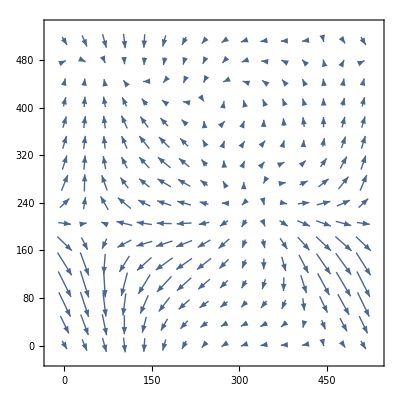

```mathematica
ListVectorPlot[Table[{baseu[[x,y]],basev[[x,y]]},{x,512},{y,512}],VectorPoints->16]
```